```mathematica
Dbasic[k_, r_]:=Piecewise[{{0, r < 0}, {r + 1, 0 <= r <= k - 1}, {2 * k - (r + 1), k <= r <= 2*k - 2}, {0, r > 2*k - 2}}]
```

```mathematica
Almugh[m_, n_, s_] := Sum[Sum[Dbasic[m, b1] * Dbasic[m, m*b2 + n*b1 + m + n - 1 - 2m*n]*s^(b1+b2 - 2n + 1),{b2, 0, 2n}], {b1, 0, 2m - 2}]
Almugh[33,27,s]
```

165+990 s+2013 s^2+2970 s^3+4026 s^4+4950 s^5+5709 s^6+4950 s^7+4026 s^8+2970 s^9+2013 s^10+990 s^11+165 s^12

```mathematica
alpha[m_,n_]:=2m*n-n
gamma[m_,n_,d_,b2_]:=(m-n)*b2 + n*d
D1[m_,n_,d_,b2_] := Piecewise[{{d - b2 + 1, 0 <=d-b2<=m-2}, {2m-(d-b2)-1, m-1<=d -b2 <=2m-2}},0]
D2[m_,n_,d_,b2_]:=Piecewise[{{-alpha[m,n] + m +gamma[m,n,d,b2], alpha[m,n]-m+1<=gamma[m,n,d,b2]<=alpha[m,n]}, {alpha[m,n] +m-gamma[m,n,d,b2], alpha[m,n]+1<=gamma[m,n,d,b2]<=alpha[m,n]+m-1}},0]
```

```mathematica
LukeAndVik[m_, n_, s_]:=Sum[Sum[D1[m, n, k+2n-1,b2]*D2[m,n,k+2n-1,b2],{b2, 0, 2n}]*s^k,{k,0,2m-2n}]
```

```mathematica
LukeAndVik[3,2, s]
```

4+19 s+4 s^2

```mathematica
Ej[m_,n_,j_]:=Floor[((j+1)*n-1)/m]
Fj[m_,n_,j_,s_]:=(j+1)*s^n+(m-j-1)*s^m
Gj[m_,n_,j_,s_]:=n*(j+1-m/n*Ej[m,n,j])+n*(m/n + m/n*Ej[m,n,j] - j - 1)*s
```

```mathematica
Luke[m_,n_,s_]:=Simplify[Sum[Fj[m,n,j,s]*Gj[m,n,j,s]*s^(j+n-1-Ej[m,n,j]),{j,0,m-1}]] /s^(2n-1)
```

```mathematica
Luke[3,2,s]
```

4+19 s+4 s^2

```mathematica
SubKernels[m_,n_,s_]:=Table[Expand[Simplify[Fj[m,n,j,s]*Gj[m,n,j,s]*s^(j+n-1-Ej[m,n,j])]/s^(2n-1)],{j,0,m-1}]
SubKernels[17,15,s]
```

{15+2 s+240 s^2+32 s^3,26+8 s+195 s^2+60 s^3,33+18 s+154 s^2+84 s^3,36+32 s+117 s^2+104 s^3,35+50 s+84 s^2+120 s^3,30+72 s+55 s^2+132 s^3,21+98 s+30 s^2+140 s^3,8+128 s+9 s^2+144 s^3,144 s+9 s^2+128 s^3+8 s^4,140 s+30 s^2+98 s^3+21 s^4,132 s+55 s^2+72 s^3+30 s^4,120 s+84 s^2+50 s^3+35 s^4,104 s+117 s^2+32 s^3+36 s^4,84 s+154 s^2+18 s^3+33 s^4,60 s+195 s^2+8 s^3+26 s^4,32 s+240 s^2+2 s^3+15 s^4,289 s^2}

```mathematica
(*************** Intersting thing happens when m and n share a common factor 
e.g., m=33, n=27 ***************)

Func[s_]:=Almugh[55,45,s];
Func[s]
pts=ComplexExpand[s/. Solve[Func[s]==0]]
Show[ComplexContourPlot[Arg[Func[s]],{s,1},Contours->15,ColorFunction->"Rainbow"],ComplexListPlot[pts->pts],ImageSize->Medium]
```

275+1650 s+3355 s^2+4950 s^3+6710 s^4+8250 s^5+10065 s^6+11550 s^7+13420 s^8+14850 s^9+16225 s^10+14850 s^11+13420 s^12+11550 s^13+10065 s^14+8250 s^15+6710 s^16+4950 s^17+3355 s^18+1650 s^19+275 s^20

{-1/4-(√5)/4-ⅈ √(5/8-(√5)/8),-1/4-(√5)/4-ⅈ √(5/8-(√5)/8),1/4+(√5)/4+ⅈ √(5/8-(√5)/8),1/4+(√5)/4+ⅈ √(5/8-(√5)/8),1/4-(√5)/4-ⅈ √(5/8+(√5)/8),1/4-(√5)/4-ⅈ √(5/8+(√5)/8),-1/4+(√5)/4+ⅈ √(5/8+(√5)/8),-1/4+(√5)/4+ⅈ √(5/8+(√5)/8),-1/4+(√5)/4-ⅈ √(5/8+(√5)/8),-1/4+(√5)/4-ⅈ √(5/8+(√5)/8),1/4-(√5)/4+ⅈ √(5/8+(√5)/8),1/4-(√5)/4+ⅈ √(5/8+(√5)/8),1/4+(√5)/4-ⅈ √(5/8-(√5)/8),1/4+(√5)/4-ⅈ √(5/8-(√5)/8),-1/4-(√5)/4+ⅈ √(5/8-(√5)/8),-1/4-(√5)/4+ⅈ √(5/8-(√5)/8),-1/2-1/(2 √5),-5/2-(√5)/2,-1/2+1/(2 √5),-5/2+(√5)/2}

-Graphics-

```mathematica
For[n=0,n<10,n++,Print[FullSimplify[Almugh[11n,9n,s]/Almugh[11,9,s]]]]
```

0

1

2 (1+s^2)^2

3 (1+s^2+s^4)^2

4 (1+s^2+s^4+s^6)^2

5 (1+s^2+s^4+s^6+s^8)^2

6 (1+s^2+s^4+s^6+s^8+s^10)^2

7 (1+s^2+s^4+s^6+s^8+s^10+s^12)^2

8 (1+s^2)^2 (1+s^4)^2 (1+s^8)^2

9 (1+s^2 (1+s^2) (1+s^4) (1+s^8))^2

```mathematica
(** But when we reduce the rational it is more easily handled **)
Func1[s_]:=Almugh[11,9,s]
pts=ComplexExpand[s/. Solve[Func1[s]==0]]
Show[ComplexContourPlot[Arg[Func1[s]],{s,1},Contours->15,ColorFunction->"Rainbow"],ComplexListPlot[pts->pts],ImageSize->Medium]
```

{-1/2-1/(2 √5),-5/2-(√5)/2,-1/2+1/(2 √5),-5/2+(√5)/2}

-Graphics-

```mathematica
(*** More examples ***)
187/180
Almugh[187,180,s]
pts=ComplexExpand[s/. Solve[Almugh[187,180,s]==0]]
Show[ComplexContourPlot[Arg[Almugh[187,180,s]],{s,1},Contours->15,ColorFunction->"Rainbow"],ComplexListPlot[pts->pts],ImageSize->Medium]
```

187/180

22230+133461 s+266868 s^2+400382 s^3+533870 s^4+667197 s^5+800604 s^6+889979 s^7+800604 s^8+667197 s^9+533870 s^10+400382 s^11+266868 s^12+133461 s^13+22230 s^14

{Root-3.74Root[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,1]-3.7370377689032312,Root-0.268Root[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,2]-0.2675916225201775,ⅈ Im[Root-0.920-0.443 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,3]-0.9204018003750546]+Re[Root-0.920-0.443 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,3]-0.9204018003750546],ⅈ Im[Root-0.920+0.443 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,4]-0.9204018003750546]+Re[Root-0.920+0.443 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,4]-0.9204018003750546],ⅈ Im[Root-0.882-0.425 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,5]-0.8817811070271543]+Re[Root-0.882-0.425 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,5]-0.8817811070271543],ⅈ Im[Root-0.882+0.425 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,6]-0.8817811070271543]+Re[Root-0.882+0.425 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,6]-0.8817811070271543],ⅈ Im[Root-0.227-0.994 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,7]-0.2265058314193461]+Re[Root-0.227-0.994 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,7]-0.2265058314193461],ⅈ Im[Root-0.227+0.994 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,8]-0.2265058314193461]+Re[Root-0.227+0.994 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,8]-0.2265058314193461],ⅈ Im[Root-0.218-0.956 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,9]-0.2178180342577776]+Re[Root-0.218-0.956 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,9]-0.2178180342577776],ⅈ Im[Root-0.218+0.956 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,10]-0.2178180342577776]+Re[Root-0.218+0.956 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,10]-0.2178180342577776],ⅈ Im[Root0.622-0.780 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,11]0.6221229940272861]+Re[Root0.622-0.780 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,11]0.6221229940272861],ⅈ Im[Root0.622+0.780 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,12]0.6221229940272861]+Re[Root0.622+0.780 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,12]0.6221229940272861],ⅈ Im[Root0.625-0.784 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,13]0.6248766124155727]+Re[Root0.625-0.784 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,13]0.6248766124155727],ⅈ Im[Root0.625+0.784 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,14]0.6248766124155727]+Re[Root0.625+0.784 ⅈRoot[22230+133461 #1+266868 #1^2+400382 #1^3+533870 #1^4+667197 #1^5+800604 #1^6+889979 #1^7+800604 #1^8+667197 #1^9+533870 #1^10+400382 #1^11+266868 #1^12+133461 #1^13+22230 #1^14&,14]0.6248766124155727]}

-Graphics-

```mathematica
(** Situation where m = n+1, so k=1 **)
```

```mathematica
For[n=0,n<10,n++,Print[Almugh[n+1,n,s]]]
```

s

1+6 s+s^2

4+19 s+4 s^2

10+44 s+10 s^2

20+85 s+20 s^2

35+146 s+35 s^2

56+231 s+56 s^2

84+344 s+84 s^2

120+489 s+120 s^2

165+670 s+165 s^2

```mathematica
Almugh[19,18,s]
pts=ComplexExpand[s/. Solve[Almugh[19,18,s]==0]]
Show[ComplexContourPlot[Arg[Almugh[19,18,s]],{s,1},Contours->15,ColorFunction->"Rainbow"],ComplexListPlot[pts->pts],ImageSize->Medium]
```

1140+4579 s+1140 s^2

{-15/4,-4/15}

-Graphics-

```mathematica
For[n=0,n<20,n++,Print[Solve[Almugh[2n+1,2n-1,s]==0]//N]]
```

{{}}

{{s→-2.72474-1.57313 ⅈ},{s→-2.72474+1.57313 ⅈ},{s→-0.275255-0.158919 ⅈ},{s→-0.275255+0.158919 ⅈ}}

{{s→-2.61803},{s→-2.61803},{s→-0.381966},{s→-0.381966}}

{{s→-1.70711},{s→-3.41421},{s→-0.292893},{s→-0.585786}}

{{s→-3.5554},{s→-1.49399},{s→-0.669347},{s→-0.281263}}

{{s→-0.723607},{s→-3.61803},{s→-0.276393},{s→-1.38197}}

{{s→-3.652},{s→-1.31196},{s→-0.762216},{s→-0.273823}}

{{s→-3.67263},{s→-1.26387},{s→-0.791224},{s→-0.272285}}

{{s→-1.22871},{s→-3.68614},{s→-0.271286},{s→-0.813859}}

{{s→-3.69549},{s→-1.20187},{s→-0.832033},{s→-0.2706}}

{{s→-3.70224},{s→-1.1807},{s→-0.846955},{s→-0.270107}}

{{s→-3.70727},{s→-1.16356},{s→-0.859431},{s→-0.26974}}

{{s→-3.71112},{s→-1.1494},{s→-0.870019},{s→-0.26946}}

{{s→-3.71414},{s→-1.1375},{s→-0.879118},{s→-0.269242}}

{{s→-3.71654},{s→-1.12737},{s→-0.887024},{s→-0.269067}}

{{s→-3.71849},{s→-1.11862},{s→-0.893957},{s→-0.268926}}

{{s→-3.7201},{s→-1.111},{s→-0.900086},{s→-0.26881}}

{{s→-3.72143},{s→-1.10431},{s→-0.905545},{s→-0.268714}}

{{s→-3.72256},{s→-1.09837},{s→-0.910436},{s→-0.268633}}

{{s→-3.72351},{s→-1.09308},{s→-0.914846},{s→-0.268564}}

```mathematica
√3-2//N
```

-0.267949

```mathematica
(** In this case of (k=1) the coefficient formulas can be written in a simple closed form expression
We'll verify that the desired polynomial is

N[n,s] = T0[n] + T1[n]s + T0[n] s^2 

where T0 and T1 are defined below.
**)
T0[n_]:=∑_(j=1)^n (j(n+1-j))
T1[n_]:=∑_(j=0)^n (j^2+(j+1)^2)
```

```mathematica
T0[N]
T1[N]
```

1/6 N (1+N) (2+N)

1/3 (1+N) (3+4 N+2 N^2)

```mathematica
For[n=0,n<10,n++,Print[Almugh[n+1,n,s]]]
For[n=0,n<10,n++,Print[{T0[n],T1[n],T0[n]}]]
```

s

1+6 s+s^2

4+19 s+4 s^2

10+44 s+10 s^2

20+85 s+20 s^2

35+146 s+35 s^2

56+231 s+56 s^2

84+344 s+84 s^2

120+489 s+120 s^2

165+670 s+165 s^2

{0,1,0}

{1,6,1}

{4,19,4}

{10,44,10}

{20,85,20}

{35,146,35}

{56,231,56}

{84,344,84}

{120,489,120}

{165,670,165}

```mathematica
(** Now obtain an algberaic formula for the root inside the unit circle **)
Assuming[N∈PositiveIntegers,FullSimplify[(-T1[N]+√(T1[N]^2-4 T0[N]^2))/(2T0[N])]]
```

(-3+√(9+3 N (2+N))+N (-4-2 N+√(9+3 N (2+N))))/(N (2+N))

```mathematica
Rt1[N_]:=(-3+√(9+3 N (2+N))+N (-4-2 N+√(9+3 N (2+N))))/(N (2+N))
```

```mathematica
For[n=1,n<10,n++,Print[Rt1[n]//N]]
```

-0.171573

-0.220789

-0.240408

-0.25

-0.255358

-0.258641

-0.260794

-0.26228

-0.263348

```mathematica
Limit[Rt1[N],N->∞]
```

```mathematica
-2+√3//N
```

-0.267949

```mathematica
(********** m = n+2, i.e., k=2 case **************)
```

```mathematica
For[n=1,n<10,n++,Print[Almugh[2n+1,2n-1,s]]]
```

1+6 s+13 s^2+6 s^3+s^4

5+30 s+55 s^2+30 s^3+5 s^4

14+84 s+147 s^2+84 s^3+14 s^4

30+180 s+309 s^2+180 s^3+30 s^4

55+330 s+561 s^2+330 s^3+55 s^4

91+546 s+923 s^2+546 s^3+91 s^4

140+840 s+1415 s^2+840 s^3+140 s^4

204+1224 s+2057 s^2+1224 s^3+204 s^4

285+1710 s+2869 s^2+1710 s^3+285 s^4

```mathematica
C0[n_]:=∑_(j=1)^n (j(2n-2j+1))
C1[n_]:=∑_(j=1)^n (j(2j))+∑_(j=1)^n ((j+n)(2n-2j+2))
C2[n_]:=(2n+1)^2+2∑_(j=1)^n ((n+j)(2j-1))
FullSimplify[C0[N]]
FullSimplify[C1[N]]
FullSimplify[C2[N]]
```

1/6 N (1+N) (1+2 N)

N (1+N) (1+2 N)

1/3 (1+2 N) (3+5 N (1+N))

```mathematica
For[n=1,n<10,n++,Print[Almugh[2n+1,2n-1,s]]]
For[n=1,n<10,n++,Print[{C0[n],C1[n],C2[n],C1[n],C0[n]}]]
```

1+6 s+13 s^2+6 s^3+s^4

5+30 s+55 s^2+30 s^3+5 s^4

14+84 s+147 s^2+84 s^3+14 s^4

30+180 s+309 s^2+180 s^3+30 s^4

55+330 s+561 s^2+330 s^3+55 s^4

91+546 s+923 s^2+546 s^3+91 s^4

140+840 s+1415 s^2+840 s^3+140 s^4

204+1224 s+2057 s^2+1224 s^3+204 s^4

285+1710 s+2869 s^2+1710 s^3+285 s^4

{1,6,13,6,1}

{5,30,55,30,5}

{14,84,147,84,14}

{30,180,309,180,30}

{55,330,561,330,55}

{91,546,923,546,91}

{140,840,1415,840,140}

{204,1224,2057,1224,204}

{285,1710,2869,1710,285}

```mathematica
(** Random plots **)
Almugh[17,15,s]
pts=ComplexExpand[s/. Solve[Almugh[17,15,s]==0]]
Show[ComplexContourPlot[Arg[Almugh[17,15,s]],{s,1},Contours->15,ColorFunction->"Rainbow"],ComplexListPlot[pts->pts],ImageSize->Medium]
```

204+1224 s+2057 s^2+1224 s^3+204 s^4

{-3/4-(√(11/3))/4,-9/4-(√33)/4,-3/4+(√(11/3))/4,-9/4+(√33)/4}

-Graphics-

```mathematica
(** Algebraically solving for roots of a palindromic quartic **)

F[A_,B_,C_,s_]:=A s^4+B s^3+C s^2+B s + A
t1[A_,B_,C_]:=(-B+√(B^2-4A C +8 A^2))/(2A)
t2[A_,B_,C_]:=(-B-√(B^2-4A C +8 A^2))/(2A)
s1[t_]:=(t+√(t^2-4))/2
s2[t_]:=(t-√(t^2-4))/2
```

```mathematica
Assuming[A>0&&B>0&&C>0,FullSimplify[s1[t1[A,B,C]]]]
Assuming[A>0&&B>0&&C>0,FullSimplify[s1[t2[A,B,C]]]]
Assuming[A>0&&B>0&&C>0,FullSimplify[s2[t1[A,B,C]]]]
Assuming[A>0&&B>0&&C>0,FullSimplify[s2[t2[A,B,C]]]]
```

(-B+√(8 A^2+B^2-4 A C)+√(-4 A (2 A+C)+2 B (B-√(8 A^2+B^2-4 A C))))/(4 A)

-(B+√(8 A^2+B^2-4 A C)-√(-4 A (2 A+C)+2 B (B+√(8 A^2+B^2-4 A C))))/(4 A)

-(B-√(8 A^2+B^2-4 A C)+√(-4 A (2 A+C)+2 B (B-√(8 A^2+B^2-4 A C))))/(4 A)

-(B+√(8 A^2+B^2-4 A C)+√(-4 A (2 A+C)+2 B (B+√(8 A^2+B^2-4 A C))))/(4 A)

```mathematica
(** Check that these are actually the roots **)
Assuming[A>0&&B>0&&C>0,FullSimplify[F[A,B,C,s1[t1[A,B,C]]]]]
Assuming[A>0&&B>0&&C>0,FullSimplify[F[A,B,C,s1[t2[A,B,C]]]]]
Assuming[A>0&&B>0&&C>0,FullSimplify[F[A,B,C,s2[t1[A,B,C]]]]]
Assuming[A>0&&B>0&&C>0,FullSimplify[F[A,B,C,s2[t2[A,B,C]]]]]
```

0

0

0

«1 more identical outputs»

```mathematica
Q11[N_]:=s1[t1[C0[N],C1[N],C2[N]]]
Q12[N_]:=s1[t2[C0[N],C1[N],C2[N]]]
Q21[N_]:=s2[t1[C0[N],C1[N],C2[N]]]
Q22[N_]:=s2[t2[C0[N],C1[N],C2[N]]]
```

```mathematica
FullSimplify[Q11[N]]
FullSimplify[Q12[N]]
FullSimplify[Q21[N]]
FullSimplify[Q22[N]]
```

((-2+N) (3+N) (1+2 N))/(2 √((-2+N) N (1+N) (3+N) (1+2 N)^2))+1/2 (-3+√6 √(-(1+N-3 N^2-2 N^3+√((-2+N) N (1+N) (3+N) (1+2 N)^2))/(N (1+N) (1+2 N))))

-((-2+N) (3+N) (1+2 N))/(2 √((-2+N) N (1+N) (3+N) (1+2 N)^2))+1/2 (-3+√6 √((-1+√((-2+N) N (1+N) (3+N) (1+2 N)^2)+N (-1+N (3+2 N)))/(N (1+N) (1+2 N))))

((-2+N) (3+N) (1+2 N))/(2 √((-2+N) N (1+N) (3+N) (1+2 N)^2))+1/2 (-3-√6 √(-(1+N-3 N^2-2 N^3+√((-2+N) N (1+N) (3+N) (1+2 N)^2))/(N (1+N) (1+2 N))))

-((-2+N) (3+N) (1+2 N))/(2 √((-2+N) N (1+N) (3+N) (1+2 N)^2))+1/2 (-3-√6 √((-1+√((-2+N) N (1+N) (3+N) (1+2 N)^2)+N (-1+N (3+2 N)))/(N (1+N) (1+2 N))))

```mathematica
Limit[s1[t1[C0[N],C1[N],C2[N]]],N->∞]
Limit[s1[t2[C0[N],C1[N],C2[N]]],N->∞]
Limit[s2[t1[C0[N],C1[N],C2[N]]],N->∞]
Limit[s2[t2[C0[N],C1[N],C2[N]]],N->∞]
```

-1

-2+√3

-1

-2-√3

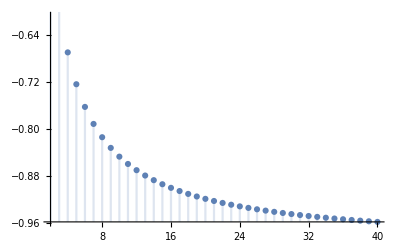

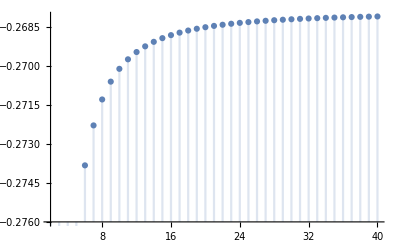

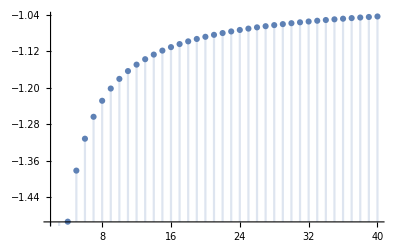

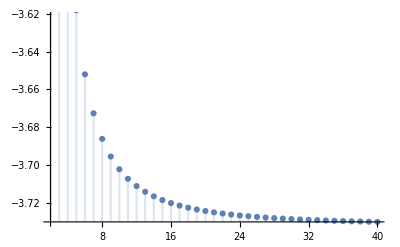

```mathematica
DiscretePlot[Q11[s],{s,2,40}]
DiscretePlot[Q12[s],{s,2,40}]
DiscretePlot[Q21[s],{s,2,40}]
DiscretePlot[Q22[s],{s,2,40}]
```

```mathematica
FullSimplify[Q12[5]]
```

1/10 (-5+√5)

```mathematica
FullSimplify[Q12[N]]
```

-((-2+N) (3+N) (1+2 N))/(2 √((-2+N) N (1+N) (3+N) (1+2 N)^2))+1/2 (-3+√6 √((-1+√((-2+N) N (1+N) (3+N) (1+2 N)^2)+N (-1+N (3+2 N)))/(N (1+N) (1+2 N))))

```mathematica
Assuming[N>0,FullSimplify[-((-2+N) (3+N) (1+2 N))/(2 √((-2+N) N (1+N) (3+N) (1+2 N)^2))]]
Assuming[N>0,FullSimplify[(-1+√((-2+N) N (1+N) (3+N) (1+2 N)^2)+N (-1+N (3+2 N)))/(N (1+N) (1+2 N))]]
```

-((-2+N) (3+N))/(2 √((-2+N) N (1+N) (3+N)))

(-1+N+N^2+√((-2+N) N (1+N) (3+N)))/(N (1+N))

```mathematica
QQ12[N]:=-((-2+N) (3+N))/(2 √((-2+N) N (1+N) (3+N)))+1/2 (-3+√6 √((-1+N+N^2+√((-2+N) N (1+N) (3+N)))/(N (1+N))))
```

```mathematica
Apart[QQ12[N]]
```

-3/2-(√(N (-6-5 N+2 N^2+N^3)))/(2 N)+(√(N (-6-5 N+2 N^2+N^3)))/(2 (1+N))+√(3/2) √((-1+N+N^2+√(N (-6-5 N+2 N^2+N^3)))/(N (1+N)))

```mathematica
Limit[-3/2-(√(N (-6-5 N+2 N^2+N^3)))/(2 N)+(√(N (-6-5 N+2 N^2+N^3)))/(2 (1+N))+√(3/2) √((-1+N+N^2+√(N (-6-5 N+2 N^2+N^3)))/(N (1+N))),N->∞]
```

-2+√3

```mathematica
(** Limiting Function for (n + k)/n **)
(** **)
```

```mathematica
Limiting[k_, s_] := Expand[Sum[s^j, {j, 0, k -1}]^2 * (s-(-2+Sqrt[3]))(s-(-2-Sqrt[3])) ]
```

```mathematica
For[k =1, k < 11, k++, Print[Limiting[k, s]]]
```

1+4 s+s^2

1+6 s+10 s^2+6 s^3+s^4

1+6 s+12 s^2+16 s^3+12 s^4+6 s^5+s^6

1+6 s+12 s^2+18 s^3+22 s^4+18 s^5+12 s^6+6 s^7+s^8

1+6 s+12 s^2+18 s^3+24 s^4+28 s^5+24 s^6+18 s^7+12 s^8+6 s^9+s^10

1+6 s+12 s^2+18 s^3+24 s^4+30 s^5+34 s^6+30 s^7+24 s^8+18 s^9+12 s^10+6 s^11+s^12

1+6 s+12 s^2+18 s^3+24 s^4+30 s^5+36 s^6+40 s^7+36 s^8+30 s^9+24 s^10+18 s^11+12 s^12+6 s^13+s^14

1+6 s+12 s^2+18 s^3+24 s^4+30 s^5+36 s^6+42 s^7+46 s^8+42 s^9+36 s^10+30 s^11+24 s^12+18 s^13+12 s^14+6 s^15+s^16

1+6 s+12 s^2+18 s^3+24 s^4+30 s^5+36 s^6+42 s^7+48 s^8+52 s^9+48 s^10+42 s^11+36 s^12+30 s^13+24 s^14+18 s^15+12 s^16+6 s^17+s^18

1+6 s+12 s^2+18 s^3+24 s^4+30 s^5+36 s^6+42 s^7+48 s^8+54 s^9+58 s^10+54 s^11+48 s^12+42 s^13+36 s^14+30 s^15+24 s^16+18 s^17+12 s^18+6 s^19+s^20

```mathematica
pts=ComplexExpand[s/. Solve[Limiting[10,s]==0]]
Show[ComplexContourPlot[Arg[Limiting[10, s]],{s,1},Contours->15,ColorFunction->"Rainbow"],ComplexListPlot[pts->pts],ImageSize->Medium]
```

{-1,-1,-1/4-(√5)/4-ⅈ √(5/8-(√5)/8),-1/4-(√5)/4-ⅈ √(5/8-(√5)/8),1/4+(√5)/4+ⅈ √(5/8-(√5)/8),1/4+(√5)/4+ⅈ √(5/8-(√5)/8),1/4-(√5)/4-ⅈ √(5/8+(√5)/8),1/4-(√5)/4-ⅈ √(5/8+(√5)/8),-1/4+(√5)/4+ⅈ √(5/8+(√5)/8),-1/4+(√5)/4+ⅈ √(5/8+(√5)/8),-1/4+(√5)/4-ⅈ √(5/8+(√5)/8),-1/4+(√5)/4-ⅈ √(5/8+(√5)/8),1/4-(√5)/4+ⅈ √(5/8+(√5)/8),1/4-(√5)/4+ⅈ √(5/8+(√5)/8),1/4+(√5)/4-ⅈ √(5/8-(√5)/8),1/4+(√5)/4-ⅈ √(5/8-(√5)/8),-1/4-(√5)/4+ⅈ √(5/8-(√5)/8),-1/4-(√5)/4+ⅈ √(5/8-(√5)/8),-2-√3,-2+√3}

-Graphics-

```mathematica
Limiting[3]-Almugh[4, 1, s]
Limiting[3]-Almugh[5, 2, s]
Limiting[3]-Almugh[7, 4, s]
```